## Init

```mathematica
(*rotation*)
R={{1/(√2),0,0,0,0,1/(√2),0,0},{0,1/(√2),0,0,0,0,1/(√2),0},{0,0,1/2,0,0,0,0,(√3)/2},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{-1/(√2),0,0,0,0,1/(√2),0,0},{0,-1/(√2),0,0,0,0,1/(√2),0},{0,0,(-√3)/2,0,0,0,0,1/2}};
```

```mathematica
(*Definition of the f-tensor*)
f[i_,j_,k_]:=0;

f[1,2,3]=f[2,3,1]=f[3,1,2]=1;
 
f[1,3,2]=f[2,1,3]=f[3,2,1]=-1;

f[1,4,7]= f[4,7,1]=f[7,1,4]=
f[1,6,5]=f[6,5,1]=f[5,1,6]=
 f[2,4,6]= f[4,6,2]= f[6,2,4]=
f[2,5,7]=f[5,7,2]=f[7,2,5]=
 f[3,4,5]= f[4,5,3]= f[5,3,4]=
 f[3,7,6]=  f[7,6,3]= f[6,3,7]=1/2;

f[1,7,4]=f[7,4,1]=f[4,1,7]=
f[1,5,6]=f[5,6,1]=f[6,1,5]=
 f[2,6,4]= f[6,4,2]= f[4,2,6]=
f[2,7,5]=f[7,5,2]=f[5,2,7]=
 f[3,5,4]= f[5,4,3]= f[4,3,5]=
 f[3,6,7]= f[6,7,3]= f[7,3,6]=-1/2;


f[4,5,8]=f[5,8,4]=f[8,4,5]=
 f[6,7,8]= f[7,8,6]= f[8,6,7]=√3/2; 

f[4,8,5]=f[8,5,4]=f[5,4,8]=
 f[6,8,7]= f[8,7,6]= f[7,6,8]=-√3/2; 

(*Definition of the d-tensor*)

d[i_,j_,k_]=0;
d[1,1,8]=d[1,8,1]=d[8,1,1]=
d[2,2,8]=d[2,8,2]=d[8,2,2]=
d[3,3,8]=d[3,8,3]=d[8,3,3]=1/(√3);
d[8,8,8]=-1/(√3);
d[1,4,6]=d[1,6,4]=d[4,1,6]=d[4,6,1]=d[6,1,4]=d[6,4,1]=
d[1,5,7]=d[1,7,5]=d[5,1,7]=d[5,7,1]=d[7,1,5]=d[7,5,1]=
d[2,5,6]=d[2,6,5]=d[5,2,6]=d[5,6,2]=d[6,2,5]=d[6,5,2]=
d[3,4,4]=d[4,3,4]=d[4,4,3]=
d[3,5,5]=d[5,3,5]=d[5,5,3]=1/2;
d[2,4,7]=d[2,7,4]=d[4,2,7]=d[4,7,2]=d[7,2,4]=d[7,4,2]=
d[3,6,6]=d[6,3,6]=d[6,6,3]=
d[3,7,7]=d[7,3,7]=d[7,7,3]=-1/2;
d[4,4,8]=d[4,8,4]=d[8,4,4]=
d[5,5,8]=d[5,8,5]=d[8,5,5]=
d[6,6,8]=d[6,8,6]=d[8,6,6]=
d[7,7,8]=d[7,8,7]=d[8,7,7]=-1/(2 √3);
```

## Constants

```mathematica
Sites=6;
```

```mathematica
tmax=20;
```

```mathematica
Nt=128;
dt=tmax/Nt;
Length[ts=N@Range[0,tmax-dt,dt]];
```

```mathematica
times=Table[t,{t,0,tmax-dt,dt}];
```

```mathematica
Runs=1000;
mSIM=10;
```

```mathematica
Uvalue=1;
μvalue=1;
Jvalue=0.01;
navgvalue=1;
```

```mathematica
putvalues:={U->Uvalue,J->Jvalue,navg->navgvalue,μ->μvalue};
```

## QM

### Diagonalizing

```mathematica
Jx=1/(√2){{0,1,0},{1,0,1},{0,1,0}};
Jy=1/(√2){{0,-ⅈ,0},{ⅈ,0,-ⅈ},{0,ⅈ,0}};
Jz={{1,0,0},{0,0,0},{0,0,-1}};
```

```mathematica
SxBasis=Table[Normalize[Eigenvectors[Jx][[n]]],{n,1,3}];
```

```mathematica
JxS=Table[SparseArray[Flatten[TensorProduct[IdentityMatrix[3^(n-1)],Jx,IdentityMatrix[3^(Sites-n)]],{{1,3,5},{2,4,6}}]],{n,1,Sites}];
JyS=Table[SparseArray[Flatten[TensorProduct[IdentityMatrix[3^(n-1)],Jy,IdentityMatrix[3^(Sites-n)]],{{1,3,5},{2,4,6}}]],{n,1,Sites}];JzS=Table[SparseArray[Flatten[TensorProduct[IdentityMatrix[3^(n-1)],Jz,IdentityMatrix[3^(Sites-n)]],{{1,3,5},{2,4,6}}]],{n,1,Sites}];
```

```mathematica
(*HQM=Sum[U/2 JzS[[n]].JzS[[n]]-μ JzS[[n]],{n,1,Sites}]- J navg Sum[Sum[JxS[[n]].JxS[[m]]+JyS[[n]].JyS[[m]],{m,n+1,Sites}],{n,1,Sites}];*)
```

```mathematica
ProgressIndicator[Dynamic[l],{1,Sites}]
```

```mathematica
ProgressIndicator[Dynamic[n],{1,Sites}]
```

```mathematica
ProgressIndicator[Dynamic[m],{1,Sites}]
```

```mathematica
Timing[HQM=Sum[Uvalue/2 JzS[[l]].JzS[[l]]-μvalue JzS[[l]],{l,1,Sites}]- Jvalue navgvalue Sum[Sum[Flatten[TensorProduct[IdentityMatrix[3^(n-1)],Jx+Jy,IdentityMatrix[3^(m-n-1)],Jx+Jy,IdentityMatrix[3^(Sites-m)]],{{1,3,5,7,9},{2,4,6,8,10}}],{m,n+1,Sites}],{n,1,Sites}];]
```

{26.93137,Null}

```mathematica
(*Timing[{En,ψn}=Eigensystem[HQM];]*)
```

```mathematica
Timing[{En,ψn}=Eigensystem[HQM];]
```

{3.64246,Null}

```mathematica
cn=Array[c,3^Sites];
```

```mathematica
Ψ=Sum[cn[[n]] ψn[[n]] ⅇ^(-ⅈ En[[n]] t),{n,1,3^Sites}];
```

### Initial conditons

```mathematica
AvgSx[n_,time_]:=Ψ*.JxS[[n]].Ψ/.t->time;
AvgSy[n_,time_]:=Ψ*.JyS[[n]].Ψ/.t->time;
AvgSz[n_,time_]:=Ψ*.JzS[[n]].Ψ/.t->time;
```

```mathematica
cn2[f_,s_]:=Abs[Flatten[UnitVector[3,f+2]⊗UnitVector[3,s+2]].Ψ]^2;
```

```mathematica
szpp=Solve[Flatten[{1,0,0}⊗{1,0,0}]==Sum[cn[[n]] ψn[[n]] ,{n,1,9}],cn];
```

```mathematica
szpm=Solve[Flatten[{1,0,0}⊗{0,0,1}]==Sum[cn[[n]] ψn[[n]] ,{n,1,9}],cn];
```

```mathematica
szpmp=Solve[Flatten[{1,0,0}⊗{0,0,1}⊗{1,0,0}]==Sum[cn[[n]] ψn[[n]] ,{n,1,27}],cn];
```

```mathematica
szp0m=Solve[Flatten[{1,0,0}⊗{0,1,0}⊗{0,0,1}]==Sum[cn[[n]] ψn[[n]] ,{n,1,27}],cn];
```

```mathematica
szp0mp=Solve[Flatten[{1,0,0}⊗{0,1,0}⊗{0,0,1}⊗{1,0,0}]==Sum[cn[[n]] ψn[[n]] ,{n,1,81}],cn];
```

```mathematica
szp0mp0=Solve[Flatten[{1,0,0}⊗{0,1,0}⊗{0,0,1}⊗{1,0,0}⊗{0,1,0}]==Sum[cn[[n]] ψn[[n]] ,{n,1,3^Sites}],cn];
```

```mathematica
szdw=Solve[Flatten[{1,0,0}⊗{0,1,0}⊗{0,0,1}⊗{1,0,0}⊗{0,1,0}⊗{0,0,1}]==Sum[cn[[n]] ψn[[n]] ,{n,1,3^Sites}],cn];
```

```mathematica
szp0=Solve[Flatten[{1,0,0}⊗{0,1,0}]==Sum[cn[[n]] ψn[[n]] ,{n,1,9}],cn];
```

```mathematica
sz00=Solve[Flatten[{0,1,0}⊗{0,1,0}]==Sum[cn[[n]] ψn[[n]] ,{n,1,9}],cn];
```

```mathematica
sx11=Solve[Flatten[SxBasis[[2]]⊗SxBasis[[2]]]==Sum[cn[[n]] ψn[[n]] ,{n,1,9}],cn];
```

### Plotting

```mathematica
Timing[stufftp=AvgSz[1,t]/.szdw[[1]];]
```

{329.21852,Null}

```mathematica
Timing[Ψv=Ψ/.szdw[[1]];]
```

$Aborted

```mathematica
Timing[stufftoplot=Ψv*.JzS[[1]].Ψv;]
```

{1.80228,Null}

```mathematica
Timing[stufftoplot=Ψv*.JxS[[2]].Ψv;]
```

{2.47262,Null}

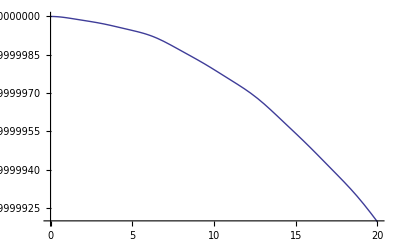
{78.8143,-Graphics-}

```mathematica
Timing[Plot[stufftoplot/.t->time,{time,0,tmax},PlotRange->All]]
```

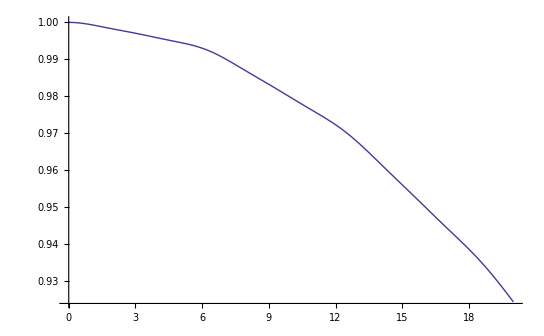
{90.36709,-Graphics-}

```mathematica
Timing[szpuj100s6=Plot[stufftp,{t,0,tmax},PlotRange->All]]
```

```mathematica
Timing[szmuj100s6=Plot[AvgSz[2,t]/.szdw[[1]],{t,0,tmax},PlotRange->All,PerformanceGoal->"Speed"]]
```

$Aborted

```mathematica
Timing[Plot[Ψv*.JzS[[1]].Ψv,{t,0,tmax},PlotRange->All]]
```

{29.50123,-Graphics-}

## Get Wig SU3

```mathematica
<<"/Users/shainen/Dropbox/Research/bhsucon/ht";
```

```mathematica
avgspins=%;
```

```mathematica
Dimensions[avgspins]
```

{128,6,8}

```mathematica
TWA6=ListPlot[{{times,2avgspins[[All,1,3]]}ᵀ,{times,2avgspins[[All,4,3]]}ᵀ},Joined->True,PlotStyle->Dotted];
```

## Get Wig SU2

```mathematica
<<"/Users/shainen/Dropbox/Research/bhsucon/su2dw6ht";
```

```mathematica
<<"/Users/shainen/Dropbox/Research/bhsucon/sofarsu2";
```

```mathematica
avgspins2=%;
```

```mathematica
Dimensions[avgspins2]
```

{128,6,3}

```mathematica
TWAsu2=ListPlot[{{times,avgspins2[[All,1,3]]}ᵀ,{times,avgspins2[[All,4,3]]}ᵀ},Joined->True,PlotStyle->Dashed];
```

## Plots

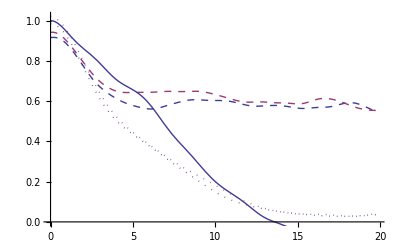

```mathematica
Show[TWA6,TWAsu2,szplus6]
```

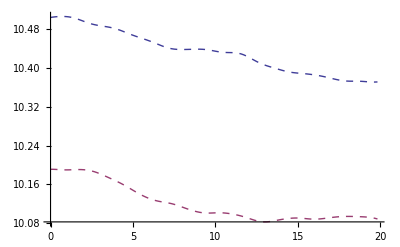

```mathematica
Show[TWAsu2]
```